# ANALYTICAL APPROACH SWT/WL - SALT CONST (4 CASES) - Phragmites australis

```mathematica
(*SAVERIO SCRIPT DATA*)

α=0.78; (* rainfall annual average depth [cm]*)
Subscript[λ, 0]=0.337;(*rainfall annual frequency [1/day]*)
Subscript[ET, max]=0.42; (* potential evapotranspiration [cm/day]*)
m=0.164; (* pore size index *)
Subscript[k, s]=1.84; (*  saturated hydraulic conductivit*)
n=0.4; (* porosity Best *)
Subscript[ψ, s]=-6 ;(* saturared matric potential*)
y0=-10;(*exterrnal water body depth [cm]*)
ymin=-61;(* minimum observed water depth*)
zr=30; (*Root zone depth[cm],depth where most of the root mass is located*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n;
Subscript[b, c]=0.0542 (*PHRAGMITES AUSTRALIS*)
Subscript[k, l] =Subscript[ET, max]/(y0-ymin-Subscript[ψ, s]);(*constant of proportionality for loamy sand soil*)
kl2=Subscript[k, l];
```

0.0542

## CASO 0 -> CT= 0 g/l C= 0 g/l

```mathematica
CT=0;(* [g/l] -> salinity stress threshold ->Red Mangrove*)
CC=0;(*salinity level [g/l]*)
```

#### PRELIMINARY EQUATIONS

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

### BELOW GROUND FUNCTION - SWT

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));(*pdf(y) with salinity effect*)
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];

I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

29.1157

#### ABOVE GROUND FUNCTION

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

3.21934

#### FINAL FUNCTION SWT/WL - normalised

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

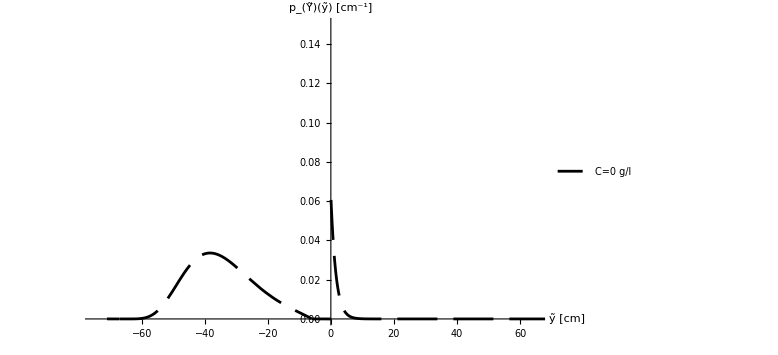

```mathematica
AnalyticalPlot0=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},
PlotStyle->{Black,Dashing[{0.05,0.02}],Thick[0.08]},
PlotLegends->Placed[{"C=0 g/l"},{0.1,0.8}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

```mathematica
Itotale=NIntegrate[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},Method->"AdaptiveMonteCarlo",PrecisionGoal->6,MaxRecursion->20]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 21 recursive bisections in z near {z} = {0.415205}. NIntegrate obtained 1.00011 and 0.0000126572 for the integral and error estimates.

1.00011

## CASO 1 -> CT = 3.55 g/l C = 3 g/l

```mathematica
CT=0;(* in quanto è come se fosse ETmax perche so sotto il limite CT*)
CC=0;(*in quanto è come se fosse ETmax perche so sotto il limite CT*)
```

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));(*pdf(y) with salinity effect*)
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];
```

```mathematica
I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

29.1157

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

3.21934

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

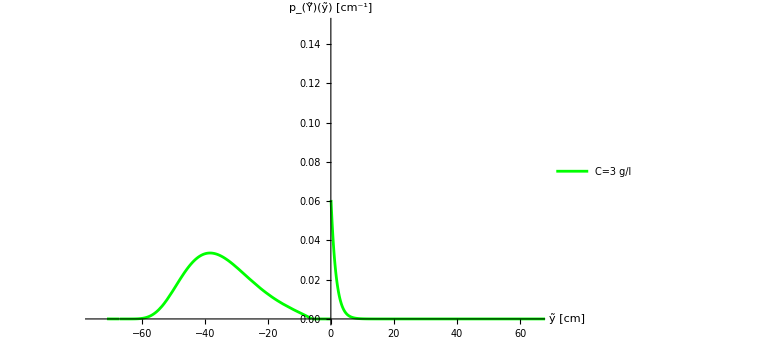

```mathematica
AnalyticalPlot1=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},
PlotStyle->{{Green,Thick[0.08]}},
PlotLegends->Placed[{"C=3 g/l"},{0.1,0.75}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

## CASO 2-> CT = 3.55 g/l C = 6 g/l

```mathematica
CT=3.55;(* [g/l] -> salinity stress threshold -*)
CC=6;(*salinity level [g/l]*)
```

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];
```

```mathematica
I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

17.6

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

4.14901

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

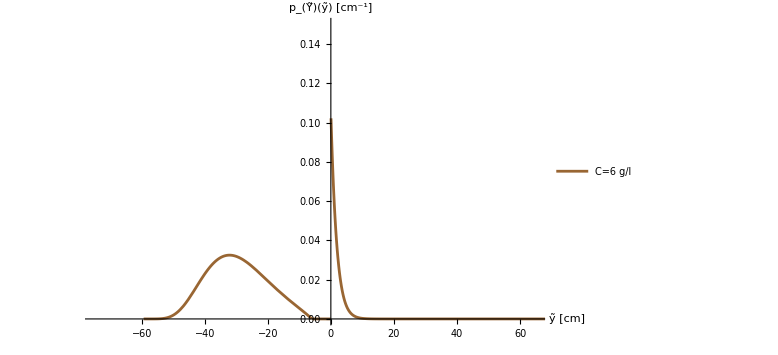

```mathematica
AnalyticalPlot2=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},
PlotStyle->{{Brown,Thick[0.08]}},
PlotLegends->Placed[{"C=6 g/l"},{0.1,0.7}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

## CASO 3 -> CT = 3.55 g/l C = 12 g/l

```mathematica
CT=3.55;
CC=12;
```

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));(*pdf(y) with salinity effect*)
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];
```

```mathematica
I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

7.09535

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

12.6138

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

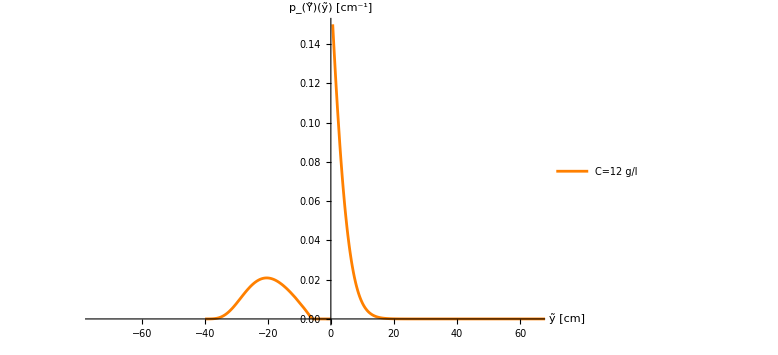

```mathematica
AnalyticalPlot3=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-5,100},
PlotStyle->{{Orange,Thick[0.08]}},
PlotLegends->Placed[{"C=12 g/l"},{0.1,0.65}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

```mathematica
Itotale=NIntegrate[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},Method->"AdaptiveMonteCarlo",PrecisionGoal->6,MaxRecursion->20]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 21 recursive bisections in z near {z} = {0.309842}. NIntegrate obtained 1.00168 and 0.0000371169 for the integral and error estimates.

1.00168

## CASO 4-> CT = 3.55 g/l C = 18 g/l

```mathematica
CT=3.55;
CC=18;
```

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));(*pdf(y) with salinity effect*)
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];
```

```mathematica
I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

3.21843

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

3697.54

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

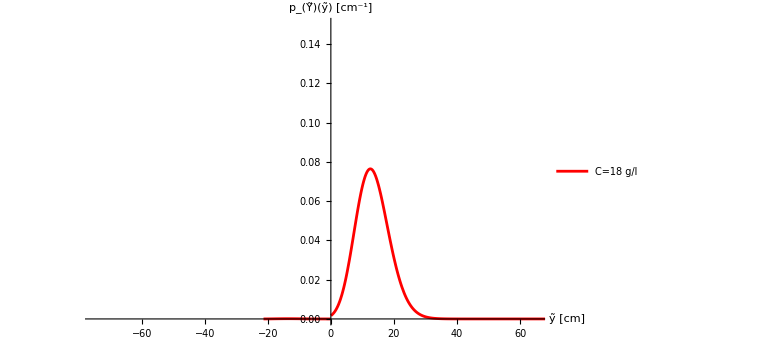

```mathematica
AnalyticalPlot4=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-5,100},
PlotStyle->{{Red,Thick[0.08]}},
PlotLegends->Placed[{"C=18 g/l"},{0.1,0.6}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

```mathematica
Itotale=NIntegrate[PFinal[z]/(I0+I1),{z,ylim[CC]-10,100},Method->"AdaptiveMonteCarlo",PrecisionGoal->6,MaxRecursion->20]
```

0.999864

## CASO 5 -> CT = 3.55 g/l C = 24 g/l

```mathematica
CT=3.55;
CC=24;
```

```mathematica
ψfc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m) (*Function defining matric potential as a function of salinity*)

ETmaxC[CC_]:=Subscript[ET, max]*(1+V*Subscript[b, c] CT-V*Subscript[b, c] CC) (*Function defining ETmax as a function of salinity (C)*)
sfcc[CC_]:=((0.05*ETmaxC[CC])/Subscript[k, s])^(m/(2+3m))(*soil moistute field capacity with salinity effect[-]*)
vc[CC_]:=ETmaxC[CC]/(1+c0*zr);
ycc[CC_]:=Subscript[ψ, s]*sfcc[CC]^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s] sfcc[CC]^(-(2+3 m)/m)]-Subscript[ψ, s]*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),(-vc[CC])/Subscript[k, s]](*critical value of water depth with salinity effect*)
βc[y_,CC_]:=n-n(1+((sfcc[CC])^(-1/(2m))-1)*(y/ycc[CC]))^(-2m);(* yield with salinity effect*)
fc[y_,CC_]:=(Subscript[k, l](y0-y-Subscript[ψ, s])-ETmaxC[CC])/βc[y,C];
gc[y_,CC_]:=1/βc[y,C];
ylim[CC_]:=y0-Subscript[ψ, s]-(ETmaxC[CC]/Subscript[k, l])
```

```mathematica
Subscript[Subscript[p, Y], c][y_,CC_]:=1/(ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])) ⅇ^(-(n (y+(sfcc[CC]^(1/(2 m)) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(sfcc[CC]^(1/(2 m)) (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(1-2 m) ycc[CC])/((-1+2 m) (-1+sfcc[CC]^(1/(2 m))))-(α Log[ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])] Subscript[λ, 0])/Subscript[k, l]-((1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m) α Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC](-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s])))] Subscript[λ, 0] ((((-1+sfcc[CC]^(1/(2 m))) y-sfcc[CC]^(1/(2 m)) ycc[CC]) Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (y-y0+Subscript[ψ, s]))))^(2 m))/(2 m Subscript[k, l])+(α Subscript[λ, 0] (2 m Log[ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])]+Hypergeometric2F1[2 m,2 m,1+2 m,(ETmaxC[CC] (-1+sfcc[CC]^(1/(2 m)))+Subscript[k, l] (y0-sfcc[CC]^(1/(2 m)) y0+sfcc[CC]^(1/(2 m)) ycc[CC]+(-1+sfcc[CC]^(1/(2 m))) Subscript[ψ, s]))/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s])))] (-(sfcc[CC]^(1/(2 m)) ycc[CC] Subscript[k, l])/((-1+sfcc[CC]^(1/(2 m))) (ETmaxC[CC]+Subscript[k, l] (-y0+Subscript[ψ, s]))))^(2 m)))/(2 m Subscript[k, l])))/α) (n-n (1+((-1+sfcc[CC]^(-1/(2 m))) y)/ycc[CC])^(-2 m));
```

```mathematica
pYNC[z_,CC_]=Re[Subscript[Subscript[p, Y], c][y,CC]/.y->(z-Subscript[ψ, s])];
```

```mathematica
I0=NIntegrate[pYNC[z,CC],{z,ylim[CC],Subscript[ψ, s]}] (*INTEGRAL OF THE FUNCTION BELOW GROUND *)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-3.82753}. NIntegrate obtained -13777.6 and 14382. for the integral and error estimates.

-13777.6

```mathematica
Integral1=∫_0^z (1/α-Subscript[λ, 0]/(ETmaxC[CC]-kl2*(y0-z)))ⅆz;
Integral2=FullSimplify[Integral1,Assumptions->{z>=0,ETmaxC>=0,kl2>=0,Subscript[λ, 0]>=0}];
ConditionalExpression[185.6449553278734+1.282051282051282 z-45.735714285714295 Log[57.92104+1. z], z>0]
Pyab[z_,CC_]:=1/(ETmaxC[CC]-kl2*(y0-z))*Exp[-Integral2];
I1=NIntegrate[Pyab[z,CC],{z,0,100}]
```

ConditionalExpression[185.645+1.28205 z-45.7357 Log[57.921+1. z], z>0]

2.16312×10^28

```mathematica
PFinal[z_]:=Piecewise[{{pYNC[z,CC],z<Subscript[ψ, s]},{Pyab[z,CC],z>0},{0,z>Subscript[ψ, s] <0}}]
```

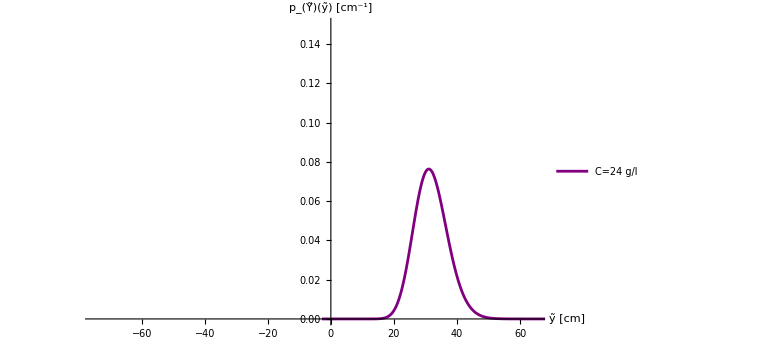

```mathematica
AnalyticalPlot5=Plot[PFinal[z]/(I0+I1),{z,ylim[CC]-5,100},
PlotStyle->{{Purple,Thick[0.08]}},
PlotLegends->Placed[{"C=24 g/l"},{0.1,0.55}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,65},{0,0.15}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)]
```

```mathematica
Itotale=NIntegrate[PFinal[z]/(I0+I1),{z,ylim[CC]-5,100},Method->"AdaptiveMonteCarlo",PrecisionGoal->6,MaxRecursion->20]
```

1.

## UNIONE GRAFICI

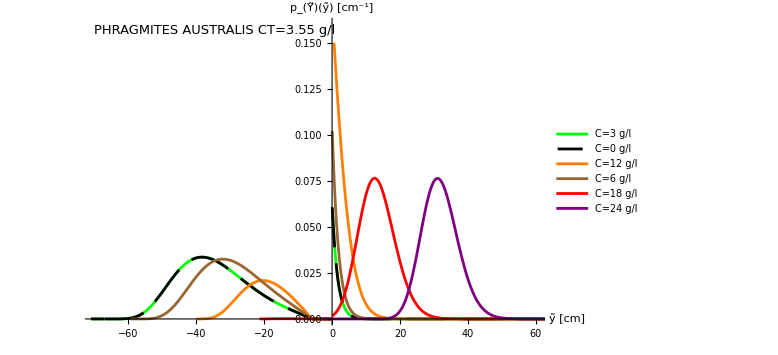

```mathematica
StrutturaPlot=Plot[{},{yi,-75,75},
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},(*Etichette degli assi*)
Epilog->{Inset[Style["PHRAGMITES AUSTRALIS CT=3.55 g/l",13],{-70,0.16},{Left,Top}]},
PlotRange->{{-70,60},{0,0.16}},(*Range degli assi*)
ImageSize->Large (*Dimensione del grafico*)];




Show[StrutturaPlot,AnalyticalPlot1, AnalyticalPlot0, AnalyticalPlot3, AnalyticalPlot2,AnalyticalPlot4,AnalyticalPlot5]
```